# 1) Potential generated by q1 located in core (ro, diel ct e1). W11: q1, q2 in core. -Graphics-

```mathematica
(* Charge q1 in the inside sphere of radius ro and diel ct e1 *)
FullSimplify[Solve[{q1*(ct/e1)*s1^n/ro^(n+1)+a*ro^n==b*ro^n+c/ro^(n+1),
-(n+1)*q1*ct*s1^n/ro^(n+2)+n*e1*a*ro^(n-1)==n*e2*b*ro^(n-1)-(n+1)*e2*c/ro^(n+2),
b*R^n+c/R^(n+1)==d/R^(n+1),
n*e2*b*R^(n-1)-(n+1)*e2*c/R^(n+2)==-(n+1)*e3*d/R^(n+2)},{a,b,c,d}],Assumptions:>{ro>0,R>0,s1>0,s2>0}]
(* ct->(4 Subscript[πϵ, 0])^-1*)
```

{{a→(ct (1+n) q1 ((e1-e2) (e3+(e2+e3) n) R^(1+2 n)+(e2-e3) (e1+(e1+e2) n) ro^(1+2 n)) s1^n)/(e1 (e1-e2) (e2-e3) n (1+n) ro^(2+4 n)+e1 (e2+(e1+e2) n) (e3+(e2+e3) n) R ro (R ro)^(2 n)),b→(ct (e2-e3) (1+n) (1+2 n) q1 s1^n)/((e2+(e1+e2) n) (e3+(e2+e3) n) R^(1+2 n)+(e1-e2) (e2-e3) n (1+n) ro^(1+2 n)),c→(ct (1+2 n) (e3+(e2+e3) n) q1 R^(1+2 n) s1^n)/((e2+(e1+e2) n) (e3+(e2+e3) n) R^(1+2 n)+(e1-e2) (e2-e3) n (1+n) ro^(1+2 n)),d→(ct e2 (1+2 n)^2 q1 R^(1+2 n) s1^n)/((e2+(e1+e2) n) (e3+(e2+e3) n) R^(1+2 n)+(e1-e2) (e2-e3) n (1+n) ro^(1+2 n))}}

```mathematica
(*
A1p[n_]:=1/(e2+(e1+e2) n)ct (1+n) q1 (((e1-e2) ro^(-1-2 n))/e1+(e2 (e2-e3) (1+2 n)^2)/((e2+(e1+e2) n) (e3+(e2+e3) n) R^(1+2 n)+(e1-e2) (e2-e3) n (1+n) ro^(1+2 n))) s1^n;
B1p[n_]:=(ct (e2-e3) (1+n) (1+2 n) q1 s1^n)/((e2+(e1+e2) n) (e3+(e2+e3) n) R^(1+2 n)+(e1-e2) (e2-e3) n (1+n) ro^(1+2 n));
C1p[n_]:=(ct (1+2 n) (e3+(e2+e3) n) q1 R^(1+2 n) s1^n)/((e2+(e1+e2) n) (e3+(e2+e3) n) R^(1+2 n)+(e1-e2) (e2-e3) n (1+n) ro^(1+2 n));
D1p[n_]:=(ct e2 (1+2 n)^2 q1 R^(1+2 n) s1^n)/((e2+(e1+e2) n) (e3+(e2+e3) n) R^(1+2 n)+(e1-e2) (e2-e3) n (1+n) ro^(1+2 n));
*)
```

```mathematica
A1[n_]:=(ct  q1 s1^n)/R^(1+2 n)PereA1equiv[n]; B1[n_]:=(ct q1 s1^n)/R^(1+2 n)PereB1equiv[n]; 
C1[n_]:=ct q1  s1^n PereC1equiv[n]; D1[n_]:=ct q1  s1^n PereD1equiv[n];
PereA1equiv[n_]:=(1/(e1* Dn[n])(1+n)((e1-e2) (e3+(e2+e3) n) R^(1+2 n)/ro^(1+2 n)+(e2-e3) (e1+(e1+e2) n)) )^1;
PereB1equiv[n_]:=(((1+2 n)(1+n)  (e2-e3))/Dn[n])^1;
PereC1equiv[n_]:=(((1+2 n) (e3+(e2+e3) n))/Dn[n])^1;
PereD1equiv[n_]:=((e2 (1+2 n)^2)/Dn[n])^1;
Dn[n_]:=(e2+(e1+e2) n) (e3+(e2+e3) n) +(e1-e2) (e2-e3) n (1+n) ro^(1+2 n)/R^(1+2 n);
(*Simplify[A1p[n]- A1[n]]
Simplify[B1p[n]- B1[n]]
Simplify[C1p[n]- C1[n]]
Simplify[D1p[n]- D1[n]]*)
```

```mathematica
(*Print["Dn(n)= ",Dn[n]/.e1->Subscript[ϵ, 1]/.e2->Subscript[ϵ, 2]/.e3->Subscript[ϵ, 3]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ro->Subscript[r, 0]];
(*Clear[Dn];*)
Print["PereA1equiv[n]= ",PereA1equiv[n]/.e1->Subscript[ϵ, 1]/.e2->Subscript[ϵ, 2]/.e3->Subscript[ϵ, 3]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ro->Subscript[r, 0]];
Print["PereB1equiv[n]= ",PereB1equiv[n]/.e1->Subscript[ϵ, 1]/.e2->Subscript[ϵ, 2]/.e3->Subscript[ϵ, 3]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ro->Subscript[r, 0]];
Print["PereC1equiv[n]= ",PereC1equiv[n]/.e1->Subscript[ϵ, 1]/.e2->Subscript[ϵ, 2]/.e3->Subscript[ϵ, 3]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ro->Subscript[r, 0]];
Print["PereD1equiv[n]= ",PereD1equiv[n]/.e1->Subscript[ϵ, 1]/.e2->Subscript[ϵ, 2]/.e3->Subscript[ϵ, 3]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ro->Subscript[r, 0]];*)
```

```mathematica
(*Polarization energy*)
W11=ct*(-1/(eps1*(se-sh))+PereA1equiv[n]/R^(2*n+1)*((se^(2n)+sh^(2n))/2-se^n sh^n*Pn));

W11/.e2->e1
```

ct (-1/(eps1 (se-sh))+((e1-e3) (1+n) R^(-1-2 n) (-Pn se^n sh^n+1/2 (se^(2 n)+sh^(2 n))))/(e1 (e3+(e1+e3) n)))

# 2) Check for 1)

## 2.1 Potential for core ro=R; Brus problem -Graphics-

```mathematica
Print["Dn(n)= ",Dn[n]/.e1->Subscript[ϵ, 1]/.e2->Subscript[ϵ, 2]/.e3->Subscript[ϵ, 2]];
Print["A1[n]= ",Simplify[A1[n]/.e1->Subscript[ϵ, 1]/.e2->Subscript[ϵ, 2]/.e3->Subscript[ϵ, 2]]];
Print["B1[n]= ",Simplify[B1[n]/.e1->Subscript[ϵ, 1]/.e2->Subscript[ϵ, 2]/.e3->Subscript[ϵ, 2]]];
(*Simplify[PereB1equiv[n]^-1/.e1->Subscript[ϵ, 1]/.e2->Subscript[ϵ, 2]/.e3->Subscript[ϵ, 2]]*)
Print["C1[n]= ",Simplify[C1[n]/.e1->Subscript[ϵ, 1]/.e2->Subscript[ϵ, 2]/.e3->Subscript[ϵ, 2]]];
Print["D1[n]= ",Simplify[D1[n]/.e1->Subscript[ϵ, 1]/.e2->Subscript[ϵ, 2]/.e3->Subscript[ϵ, 2]]];
```

Dn(n)= (ϵ_2+2 n ϵ_2) (ϵ_2+n (ϵ_1+ϵ_2))

A1[n]= (ct (1+n) q1 ro^(-1-2 n) s1^n (ϵ_1-ϵ_2))/(ϵ_1 (n ϵ_1+(1+n) ϵ_2))

B1[n]= 0

C1[n]= (ct (1+2 n) q1 s1^n)/(n ϵ_1+(1+n) ϵ_2)

D1[n]= (ct (1+2 n) q1 s1^n)/(n ϵ_1+(1+n) ϵ_2)

## 2.2 Check1: e3=1; e2=1 (*Same! as Bottcher p. 83 *)

```mathematica
e3=1;e2=1; 
FullSimplify[Solve[{q1*(ct/e1)*s1^n/ro^(n+1)+a*ro^n==0*q2*(ct/e2)*ro^n/s2^(n+1)+b*ro^n+c/ro^(n+1),
-(n+1)*q1*ct*s1^n/ro^(n+2)+n*e1*a*ro^(n-1)==0*n*q2*ct*ro^(n-1)/s2^(n+1)+n*e2*b*ro^(n-1)-(n+1)*e2*c/ro^(n+2),
0*q2*(ct/e2)*s2^n/R^(n+1)+b*R^n+c/R^(n+1)==d/R^(n+1),
-(n+1)*0*q2*ct*s2^n/R^(n+2)+n*e2*b*R^(n-1)-(n+1)*e2*c/R^(n+2)==-(n+1)*e3*d/R^(n+2)},{a,b,c,d}]]/.e1->Subscript[ϵ, 1]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ro->Subscript[r, 0]/.ct->(4 Subscript[πϵ, 0])^-1
```

{{a→((1+n) q1 r_0^(-1-2 n) s_1^n (-1+ϵ_1))/(4 ϵ_1 (1+n+n ϵ_1) πϵ_0),b→0,c→((1+2 n) q1 s_1^n)/(4 (1+n+n ϵ_1) πϵ_0),d→((1+2 n) q1 s_1^n)/(4 (1+n+n ϵ_1) πϵ_0)}}

```mathematica
e3=1;e2=1;
Print["A[",n,"]= ",FullSimplify[A1[n]]/.e1->Subscript[ϵ, 1]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ro->Subscript[r, 0]/.ct->(4 Subscript[πϵ, 0])^-1];
Print["B[",n,"]= ",FullSimplify[B1[n]]/.e1->Subscript[ϵ, 1]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ro->Subscript[r, 0]/.ct->(4 Subscript[πϵ, 0])^-1];
Print["C[",n,"]= ",FullSimplify[C1[n]]/.e1->Subscript[ϵ, 1]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ro->Subscript[r, 0]/.ct->(4 Subscript[πϵ, 0])^-1];
Print["D[",n,"]= ",FullSimplify[D1[n]]/.e1->Subscript[ϵ, 1]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ro->Subscript[r, 0]/.ct->(4 Subscript[πϵ, 0])^-1];
Clear[n,q1,e1,e2,e3];
```

A[n]= ((1+n) q1 r_0^(-1-2 n) s_1^n (-1+ϵ_1))/(4 ϵ_1 (1+n+n ϵ_1) πϵ_0)

B[n]= 0

C[n]= ((1+2 n) q1 s_1^n)/(4 (1+n+n ϵ_1) πϵ_0)

D[n]= ((1+2 n) q1 s_1^n)/(4 (1+n+n ϵ_1) πϵ_0)

## 2.3 Check2: e3=e2=e3

```mathematica
(*Check 2:*) e1=e2=e3;
Print["A[",n,"]= ",FullSimplify[A1[n]]/.e1->Subscript[ϵ, 1]/.e2->Subscript[ϵ, 2]/.e3->Subscript[ϵ, 3]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ro->Subscript[r, 0]/.ct->(4 Subscript[πϵ, 0])^-1];
Print["B[",n,"]= ",FullSimplify[B1[n]]/.e1->Subscript[ϵ, 1]/.e2->Subscript[ϵ, 2]/.e3->Subscript[ϵ, 3]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ro->Subscript[r, 0]/.ct->(4 Subscript[πϵ, 0])^-1];
Print["C[",n,"]= ",FullSimplify[C1[n]]/.e1->Subscript[ϵ, 1]/.e2->Subscript[ϵ, 2]/.e3->Subscript[ϵ, 3]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ro->Subscript[r, 0]/.ct->(4 Subscript[πϵ, 0])^-1];
Print["D[",n,"]= ",FullSimplify[D1[n]]/.e1->Subscript[ϵ, 1]/.e2->Subscript[ϵ, 2]/.e3->Subscript[ϵ, 3]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ro->Subscript[r, 0]/.ct->(4 Subscript[πϵ, 0])^-1];Clear[n,q1,e1,e2,e3];
```

A[n]= 0

B[n]= 0

C[n]= (q1 s_1^n)/(4 ϵ_1 πϵ_0)

D[n]= (q1 s_1^n)/(4 ϵ_1 πϵ_0)

# 3) Charge q2 in layer (ro, R and diel ct e2). W12, W22 -Graphics-

## 3.1 Potential generated by q2 located in layer.

```mathematica
(* Charge q2 in the layer of radius ro< - >R and diel ct e2 *)
Clear[a,b,c,d];FullSimplify[Solve[{a*ro^n==q2*(ct/e2)*ro^n/s2^(n+1)+b*ro^n+c/ro^(n+1),
n*e1*a*ro^(n-1)==n*q2*ct*ro^(n-1)/s2^(n+1)+n*e2*b*ro^(n-1)-(n+1)*e2*c/ro^(n+2),
q2*(ct/e2)*s2^n/R^(n+1)+b*R^n+c/R^(n+1)==d/R^(n+1),
-(n+1)*q2*ct*s2^n/R^(n+2)+n*e2*b*R^(n-1)-(n+1)*e2*c/R^(n+2)==-(n+1)*e3*d/R^(n+2)},{a,b,c,d}]]
```

{{a→(ct (1+2 n) q2 s2^(-1-n) ((e3+(e2+e3) n) R^(1+2 n)+(e2-e3) (1+n) s2^(1+2 n)))/((e2+(e1+e2) n) (e3+(e2+e3) n) R^(1+2 n)+(e1-e2) (e2-e3) n (1+n) ro^(1+2 n)),b→(ct (e2-e3) (1+n) q2 s2^(-1-n) ((-e1+e2) n ro^(1+2 n)+(e2+(e1+e2) n) s2^(1+2 n)))/(e2 ((e2+(e1+e2) n) (e3+(e2+e3) n) R^(1+2 n)+(e1-e2) (e2-e3) n (1+n) ro^(1+2 n))),c→-(ct (e1-e2) q2 ro^(1+2 n) s2^(-1-n) (n (e3+(e2+e3) n) R^(1+2 n)+(e2-e3) n (1+n) s2^(1+2 n)))/(e2 ((e2+(e1+e2) n) (e3+(e2+e3) n) R^(1+2 n)+(e1-e2) (e2-e3) n (1+n) ro^(1+2 n))),d→(ct (1+2 n) q2 R^(1+2 n) s2^(-1-n) (-((e1-e2) n ro^(1+2 n))+(e2+(e1+e2) n) s2^(1+2 n)))/((e2+(e1+e2) n) (e3+(e2+e3) n) R^(1+2 n)+(e1-e2) (e2-e3) n (1+n) ro^(1+2 n))}}

```mathematica
(*A2p[n_]:=(ct (1+2 n) q2 s2^(-1-n) ((e3+(e2+e3) n) R^(1+2 n)+(e2-e3) (1+n) s2^(1+2 n)))/((e2+(e1+e2) n) (e3+(e2+e3) n) R^(1+2 n)+(e1-e2) (e2-e3) n (1+n) ro^(1+2 n));
B2p[n_]:=(ct (e2-e3) (1+n) q2 s2^(-1-n) ((-e1+e2) n ro^(1+2 n)+(e2+(e1+e2) n) s2^(1+2 n)))/(e2 ((e2+(e1+e2) n) (e3+(e2+e3) n) R^(1+2 n)+(e1-e2) (e2-e3) n (1+n) ro^(1+2 n)));
C2p[n_]:=-(ct (e1-e2) q2 ro^(1+2 n) s2^(-1-n) (n (e3+(e2+e3) n) R^(1+2 n)+(e2-e3) n (1+n) s2^(1+2 n)))/(e2 ((e2+(e1+e2) n) (e3+(e2+e3) n) R^(1+2 n)+(e1-e2) (e2-e3) n (1+n) ro^(1+2 n)));
D2p[n_]:=(ct (1+2 n) q2 R^(1+2 n) s2^(-1-n) (-(e1-e2) n ro^(1+2 n)+(e2+(e1+e2) n) s2^(1+2 n)))/((e2+(e1+e2) n) (e3+(e2+e3) n) R^(1+2 n)+(e1-e2) (e2-e3) n (1+n) ro^(1+2 n));*)
```

```mathematica
A2[n_]:=ct* PereA2equiv[n,s2]*q2  s2^(-1-n) ; B2[n_]:=ct *PereB2equiv[n,s2]*q2  s2^(-1-n);
C2[n_]:=ct *PereC2equiv[n,s2]*q2  ro^(1+2 n) s2^(-1-n) ; D2[n_]:=ct *PereD2equiv[n,s2]*q2  ro^(1+2 n) s2^(-1-n) ;

PereA2equiv[n_,s2_]:=(1/Dn[n](1+2 n) * ((e3+(e2+e3) n) +(e2-e3) (1+n) s2^(1+2 n)/R^(1+2 n)))^1;
PereB2equiv[n_,s2_]:=(1/(e2* Dn[n])(e2-e3) (1+n)  ((-e1+e2) n ro^(1+2 n)/R^(1+2 n)+(e2+(e1+e2) n) s2^(1+2 n)/R^(1+2 n)))^1;
PereC2equiv[n_,s2_]:=(1/(e2* Dn[n])(e1-e2)   (-n (e3+(e2+e3) n) +(-e2+e3) n (1+n) s2^(1+2 n)/R^(1+2 n)))^1;
PereD2equiv[n_,s2_]:=(((1+2 n)   (-(e1-e2) n +(e2+(e1+e2) n) s2^(1+2 n)/ro^(1+2 n)))/Dn[n])^1;

Dn[n_]:=(e2+(e1+e2) n) (e3+(e2+e3) n) +(e1-e2) (e2-e3) n (1+n) ro^(1+2 n)/R^(1+2 n);

(*Simplify[A2p[n]- A2[n]]
Simplify[B2p[n]- B2[n]]
Simplify[C2p[n]- C2[n]]
Simplify[D2p[n]- D2[n]] *)

(*
Print["PereA2equiv[n]= ",PereA2equiv[n,s2]/.e1->Subscript[ϵ, 1]/.e2->Subscript[ϵ, 2]/.e3->Subscript[ϵ, 3]/.s2->Subscript[s, 2]/.s1->Subscript[s, 1]/.ro->Subscript[r, 0]];
Print["PereB2equiv[n]= ",PereB2equiv[n,s2]/.e1->Subscript[ϵ, 1]/.e2->Subscript[ϵ, 2]/.e3->Subscript[ϵ, 3]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ro->Subscript[r, 0]];
Print["PereC2equiv[n]= ",PereC2equiv[n,s2]/.e1->Subscript[ϵ, 1]/.e2->Subscript[ϵ, 2]/.e3->Subscript[ϵ, 3]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ro->Subscript[r, 0]];
Print["PereD2equiv[n]= ",PereD2equiv[n,s2]/.e1->Subscript[ϵ, 1]/.e2->Subscript[ϵ, 2]/.e3->Subscript[ϵ, 3]/.s1->Subscript[s, 1]/.s2->Subscript[s, 2]/.ro->Subscript[r, 0]];
*)
```

## 3.2 Polarization energy check: W11=W22=W12 if e1=e2.

```mathematica
AA1=Simplify[(PereB2equiv[n,se]+PereC2equiv[n,se])1/(2*se)];
AA2=Simplify[(PereB2equiv[n,sh]+PereC2equiv[n,sh])1/(2*sh)];
BB2=Pn*Simplify[(PereB2equiv[n,se]+PereC2equiv[n,sh])*sh^n/se^(n+1)+((PereB2equiv[n,sh]+PereC2equiv[n,se])se^n/sh^(n+1))]/2;
W22=ct*(-1/(eps2 (se-sh))+Simplify[(AA1+AA2-BB2)]);

Simplify[W22/.e2->e1]

W11/.e2->e1
Simplify[(W22-W11)/.e2->e1/.eps2->eps1]
```

ct (-1/(eps2 se-eps2 sh)+((e1-e3) (1+n) R^(-1-2 n) (se^(2 n)-2 Pn se^n sh^n+sh^(2 n)))/(2 e1 (e3+e1 n+e3 n)))

ct (-1/(eps1 (se-sh))+((e1-e3) (1+n) R^(-1-2 n) (-Pn se^n sh^n+1/2 (se^(2 n)+sh^(2 n))))/(e1 (e3+(e1+e3) n)))

0

```mathematica
n=0;
Simplify[W22/.e2->e1,Assumptions:>{ro>0}]
Clear[ro,n]
Limit[W22/.e2->e1,ro->0,Assumptions:>n>=0]
Limit[W22/.e2->e3,ro->0,Assumptions:>n>=0]
n=0;Limit[W22/.e2->e1,ro->0]
Clear[ro,n]
```

ct (-((e1-e3) (-1+Pn))/(e1 e3 R)-1/(eps2 se-eps2 sh))

ct (-1/(eps2 se-eps2 sh)+((e1-e3) (1+n) R^(-1-2 n) (se^(2 n)-2 Pn se^n sh^n+sh^(2 n)))/(2 e1 (e3+e1 n+e3 n)))

ct (-1/(eps2 se-eps2 sh)+((e1-e3) n se^(-1-n) sh^(-1-n) (-se^n sh^n (se+sh)+Pn (se^(1+2 n)+sh^(1+2 n))))/(2 e3 (e3+e1 n+e3 n)))

-((ct (e1 (e3 R+eps2 (-1+Pn) (se-sh))-e3 eps2 (-1+Pn) (se-sh)))/(e1 e3 eps2 R (se-sh)))

```mathematica
Limit[W22/.e2->e3,ro->0,Assumptions:>n>=0]
```

ct (-1/(eps2 se-eps2 sh)+((e1-e3) n se^(-1-n) sh^(-1-n) (-se^n sh^n (se+sh)+Pn (se^(1+2 n)+sh^(1+2 n))))/(2 e3 (e3+e1 n+e3 n)))

```mathematica
W12=ct/2*(PereA1equiv[n] sh^(2*n)/R^(2*n+1)+PereB2equiv[n,se] 1/se+PereC2equiv[n,se] ro^(2*n+1)/se^(2n+2)-Pn*((PereA2equiv[n,se]+PereC1equiv[n])sh^n/se^(n+1)+PereB1equiv[n]*R^(-2*n-1)sh^n se^n));
W12e2e1p=FullSimplify[W12/.e2->e1]
Simplify[(W11-W12)/.e2->e1/.eps2->eps1];
```

1/(2 e1 (e3+(e1+e3) n))ct R^(-1-2 n) se^(-1-n) ((e1-e3) (1+n) se^(1+3 n)-2 Pn ((e3+(e1+e3) n) R^(1+2 n)+(e1-e3) (1+n) se^(1+2 n)) sh^n+(e1-e3) (1+n) se^(1+n) sh^(2 n))

```mathematica
W12e2e1p=1/(2 e1 (e3+(e1+e3) n))ct R^(-1-2 n) se^(-1-n) ((e1-e3) (1+n) se^(1+3 n)-2 Pn ((e3+(e1+e3) n) R^(1+2 n)+(e1-e3) (1+n) se^(1+2 n)) sh^n+(e1-e3) (1+n) se^(1+n) sh^(2 n));

v3=1/(2 e1 (e3+e1 n+e3 n))ct   (R^(-1-2 n)(se^(2 n)+sh^(2 n))(1+n)(-e3+e1)+ 2 Pn  (-sh^n se^(-1-n)(e3(1+n)+n *e1)-R^(-1-2 n)(1+n)(e1-e3)se^n sh^n));
W12e2e1=1/(2 e1 (e3+e1 n+e3 n))ct   (R^(-1-2 n)(se^(2 n)+sh^(2 n))(1+n)(-e3+e1)- 2 Pn  R^(-1-2 n)(1+n)(e1-e3)se^n sh^n)+-Pn/e1 ct sh^n se^(-1-n)  ;
Simplify[W12e2e1p-W12e2e1]
```

0

# 4) Check for 3) -Graphics-

## 4.1 Check1: e3=1; e2=1 (*Same! as Bottcher p. 86 *)

```mathematica
Print["A2[n]= ",Simplify[A2[n]/.e2->1/.e3->1, Assumptions->n>=0]];
Print["B2[n]= ",Simplify[B2[n]/.e2->1/.e3->1, Assumptions->n>=0]];
Print["C2[n]= ",Simplify[C2[n]/.e2->1/.e3->1, Assumptions->n>=0]];
Print["D2[n]= ",FullSimplify[D2[n]/.e2->1/.e3->1, Assumptions->n>=0]];
```

A2[n]= (ct (1+2 n) q2 s2^(-1-n))/(1+n+e1 n)

B2[n]= 0

C2[n]= -(ct (-1+e1) n q2 ro^(1+2 n) s2^(-1-n))/(1+n+e1 n)

D2[n]= -(ct (-1+e1) n q2 ro^(1+2 n) s2^(-1-n))/(1+n+e1 n)+ct q2 s2^n

## 4.2 Check2: e3=e2=e3

```mathematica
e1=e2=e3;
Print["A2[n]= ",Simplify[A2[n], Assumptions->n>=0]];
Print["B2[n]= ",Simplify[B2[n], Assumptions->n>=0]];
Print["C2[n]= ",Simplify[C2[n], Assumptions->n>=0]];
Print["D2[n]= ",FullSimplify[D2[n], Assumptions->n>=0]];
Clear[e1,e2,e3]
```

A2[n]= (ct q2 s2^(-1-n))/e3

B2[n]= 0

C2[n]= 0

D2[n]= (ct q2 s2^n)/e3

# 5) Charge q out in environment with diel ct e3. W13 -Graphics-

## 5.1 Potential generated by q3 located in solvent.

```mathematica
V3=FullSimplify[Solve[{a*ro^n==b*ro^n+c*ro^(-n-1),n*e1*a*ro^(n-1)==n*e2*b*ro^(n-1)-(n+1)*e2*c*ro^(-n-2),b*R^n+c*R^(-n-1)==(ct/e3)*(q3/s3)*(R/s3)^n+d*R^(-n-1),n*e2*b*R^(n-1)-(n-1)*e2*c*R^(-n-2)==n*q3*ct*s3^(-n-1)*R^(n-1)-(n+1)*e3*d*R^(-n-2)},{a,b,c,d}],Assumptions:>{s3>0,ro>0,R>0}]
(*V3[[1]][[2]][[2]]*)
(*/.ct->(4 Subscript[πϵ, 0])^-1*)
```

{{a→(ct e2 (1+2 n)^2 q3 R^(1+2 n) s3^(-1-n))/((e2+(e1+e2) n) (e3+(e2+e3) n) R^(1+2 n)+(e1-e2) n (e2 (-1+n)-e3 (1+n)) ro^(1+2 n)),b→(ct (1+2 n) (e2+(e1+e2) n) q3 R^(1+2 n) s3^(-1-n))/((e2+(e1+e2) n) (e3+(e2+e3) n) R^(1+2 n)+(e1-e2) n (e2 (-1+n)-e3 (1+n)) ro^(1+2 n)),c→-((ct (e1-e2) n (1+2 n) q3 R ro (R ro)^(2 n) s3^(-1-n))/((e2+(e1+e2) n) (e3+(e2+e3) n) R^(1+2 n)+(e1-e2) n (e2 (-1+n)-e3 (1+n)) ro^(1+2 n))),d→1/s3 ct q3 R (-((R^2/s3)^n)/e3+((1+2 n) R^(2 n) ((e2+(e1+e2) n) R^(1+2 n)+(-e1+e2) n ro^(1+2 n)) s3^-n)/((e2+(e1+e2) n) (e3+(e2+e3) n) R^(1+2 n)+(e1-e2) n (e2 (-1+n)-e3 (1+n)) ro^(1+2 n)))}}

```mathematica
(*A3p[n_]:=(ct (1+2 n)^2 q3 R^(1+2 n) s3^(-1-n) e2)/(n ro^(1+2n) (e1-e2) ((-1+n) e2-(1+n) e3)+R^(1+2 n) (e2+n (e1+e2)) (e3+n (e2+e3)));
Simplify[A3p[n]-(ct (1+2 n)^2 q3  s3^(-1-n) e2)/(n ro^(1+2n)/R^(1+2 n) (e1-e2) ((-1+n) e2-(1+n) e3)+ (e2+n (e1+e2)) (e3+n (e2+e3)))]*)
(*Dn[n_]:=(e2+(e1+e2) n) (e3+(e2+e3) n) +(e1-e2) (e2-e3) n (1+n) ro^(1+2 n)/R^(1+2 n);
A3p[n_]:=V3[[1]][[1]][[2]];*)
Gn[n_]:=n ro^(1+2n)/R^(1+2 n) (e1-e2) ((-1+n) e2-(1+n) e3)+ (e2+n (e1+e2)) (e3+n (e2+e3));
A3s[n_]:=(ct (1+2 n)^2 q3  s3^(-1-n) e2)/Gn[n];(**)
A3[n_]:=(ct  q3)/s3^(1+n)PereA3equiv[n];
PereA3equiv[n_]:=((1+2 n)^2  e2)/Gn[n];
(*Simplify[A3p[n]-A3s[n]]
Simplify[A3[n]-A3s[n]]*)
```

```mathematica
(*B3p[n_]:=(ct (1+2 n) q3 R^(1+2 n) s3^(-1-n) (e2+n (e1+e2)))/(n ro^(1+2n) (e1-e2) ((-1+n) e2-(1+n) e3)+R^(1+2 n) (e2+n (e1+e2)) (e3+n (e2+e3)));
Simplify[B3p[n]-(ct (1+2 n) q3 R^(1+2 n) s3^(-1-n) (e2+n (e1+e2)))/(n ro^(1+2n) (e1-e2) ((-1+n) e2-(1+n) e3)+R^(1+2 n) (e2+n (e1+e2)) (e3+n (e2+e3)))]
B3p[n_]:=V3[[1]][[2]][[2]];*)
B3s[n_]:=ct (1+2 n) q3  s3^(-1-n) (e2+n (e1+e2))/Gn[n];
B3[n_]:=(ct  q3)/s3^(1+n) PereB3equiv[n];
PereB3equiv[n_]:=((1+2 n) (e2+n (e1+e2)))/Gn[n];
(*Simplify[B3p[n]-B3s[n]]
Simplify[B3p[n]-B3[n]]*)
```

```mathematica
(*C3p[n_]:=-(ct n (1+2 n) q3 * s3^(-1-n) ro (ro)^(2 n) (e1-e2))/(n ro^(1+2n)/R^(1+2 n) (e1-e2) ((-1+n) e2-(1+n) e3)+ (e2+n (e1+e2)) (e3+n (e2+e3)));
Simplify[C3p[n]+(ct n (1+2 n) q3 R s3^(-1-n) ro (R ro)^(2 n) (e1-e2))/(n ro^(1+2n) (e1-e2) ((-1+n) e2-(1+n) e3)+R^(1+2 n) (e2+n (e1+e2)) (e3+n (e2+e3))),Assumptions:>{s3>0,ro>0,R>0}]
C3p[n_]:=V3[[1]][[3]][[2]];*)
C3s[n_]:=-ct n (1+2 n) q3 * s3^(-1-n) *ro^(2 n+1) (e1-e2)/Gn[n];
C3[n_]:=ct  q3 ro^(2 n+1)/s3^(1+n) PereC3equiv[n];
PereC3equiv[n_]:=(n (1+2 n) (e2-e1))/Gn[n];
(*Simplify[C3p[n]-C3[n],Assumptions:>{s3>0,ro>0,R>0}]*)
```

```mathematica
(*D3p[n_]:=1/s3 ct q3 R (-((R^2/s3)^n)/e3+((1+2 n) R^(2 n) s3^-n (n ro^(1+2n) (-e1+e2)+R^(1+2 n) (e2+n (e1+e2))))/(n ro^(1+2n) (e1-e2) ((-1+n) e2-(1+n) e3)+R^(1+2 n) (e2+n (e1+e2)) (e3+n (e2+e3))));
Simplify[D3p[n]-1/s3 ct q3 R (-((R^2/s3)^n)/e3+((1+2 n) R^(2 n) s3^-n (n ro^(1+2n) (-e1+e2)+R^(1+2 n) (e2+n (e1+e2))))/(n ro^(1+2n) (e1-e2) ((-1+n) e2-(1+n) e3)+R^(1+2 n) (e2+n (e1+e2)) (e3+n (e2+e3)))),Assumptions:>{s3>0,ro>0,R>0}]

D3s[n_]:=ct *q3 *R^(2*n+1)*s3^(-n-1) (-1/e3+((1+2 n)  (n ro^(1+2n)/R^(2 n+1) (-e1+e2)+(e2+n (e1+e2))))/Gn[n]);
D3p[n_]:=V3[[1]][[4]][[2]];*)
D3[n_]:=ct  q3 R^(2 n+1)/s3^(1+n) PereD3equiv[n];
PereD3equiv[n_]:= (-1/e3+((1+2 n)  (n ro^(1+2n)/R^(2 n+1) (-e1+e2)+(e2+n (e1+e2))))/Gn[n]);
(*Simplify[PereD3equiv[n]/.e2->e1]*)
(*Simplify[D3p[n]-D3[n],Assumptions:>{s3>0,ro>0,R>0}]*)
```

## 5.1# Potential generated by q3 located in solvent-check

```mathematica
V3=FullSimplify[Solve[{a*ro^n==b*ro^n+c*ro^(-n-1),n*e1*a*ro^(n-1)==n*e2*b*ro^(n-1)-(n+1)*e2*c*ro^(-n-2),b*R^n+c*R^(-n-1)==(ct/e3)*(q3/s3)*(R/s3)^n+d*R^(-n-1),n*e2*b*R^(n-1)-(n-1)*e2*c*R^(-n-2)==n*q3*ct*s3^(-n-1)*R^(n-1)-(n+1)*e3*d*R^(-n-2)},{a,b,c,d}],Assumptions:>{s3>0,ro>0,R>0}];
A3[n_]:=q3 (ct e2 (1+2 n)^2 ) s3^(-1-n)/G[n];

B3[n_]:=q3 (ct (1+2 n) (e2+(e1+e2) n) ) s3^(-1-n)/G[n];

C3[n_]:=-q3 (ct (e1-e2) n (1+2 n) (ro)^(2 n+1) ) s3^(-1-n)/G[n];


D3[n_]:=ct q3* s3^(-1-n)*(-R^(1+2 n)/e3+1/G[n](1+2 n) *((e2+(e1+e2) n) R^(1+2 n)+(-e1+e2) n ro^(1+2 n)) );

D3[n_]:=ct q3* s3^(-1-n)*R^(1+2 n)(-G[n]  +(1+2 n) *e3*(e2+(e1+e2) n +(-e1+e2) n (ro/R)^(1+2 n)) )/(e3*G[n]);
(*G[n_]:=(e2+(e1+e2) n) (e3+(e2+e3) n) +(e1-e2) n (e2 (-1+n)-e3 (1+n)) ro^(1+2 n)/R^(1+2 n);*)
G[n_]:=n ro^(1+2n)/R^(1+2 n) (e1-e2) ((-1+n) e2-(1+n) e3)+ (e2+n (e1+e2)) (e3+n (e2+e3));
```

## 5.2 Polarization energy check: W13(e2=e1)=W12(e2=e1)

```mathematica
W13=ct/2 Simplify[((PereA1equiv[n]*sh^(2n)/R^(2 n+1)+PereD3equiv[n]*R^(2 n+1)/se^(2n+2))-(PereD1equiv[n]+PereA3equiv[n])sh^n/se^(n+1)*Pn)];
(*W31=ct/2 Simplify[((PereA1equiv[n]*se^(2n)/R^(2 n+1)+PereD3equiv[n]*R^(2 n+1)/sh^(2n+2))-(PereD1equiv[n]+PereA3equiv[n])se^n/sh^(n+1)*Pn)];
W31e2e3=Simplify[W31/.e2->e3];*)
W13e2e1=Simplify[W13/.e2->e1]
```

1/2 ct (((-e1+e3) n R^(1+2 n) se^(-2 (1+n)))/(e3 (e3+e1 n+e3 n))-(2 (1+2 n) Pn se^(-1-n) sh^n)/(e3+e1 n+e3 n)+((e1-e3) (1+n) R^(-1-2 n) sh^(2 n))/(e1 (e3+(e1+e3) n)))

```mathematica
W12e2e3=Simplify[W12/.e2->e3]
```

(ct (-((e1-e3) n ro^(1+2 n) se^(-2 (1+n)))/e3-2 (1+2 n) Pn se^(-1-n) sh^n+((e1-e3) (1+n) ro^(-1-2 n) sh^(2 n))/e1))/(2 (e3+(e1+e3) n))

```mathematica
FullSimplify[W13e2e1-W12e2e3]/.ro->R
```

0

```mathematica
Simplify[W12/.e1->ϵ/.e2->ϵ/.e3->ϵ]
Simplify[W13/.e1->ϵ/.e2->ϵ/.e3->ϵ]
```

-(ct Pn se^(-1-n) sh^n)/ϵ

-(ct Pn se^(-1-n) sh^n)/ϵ

```mathematica
Simplify[Dn[n]-Gn[n]]
```

2 (e1-e2) e2 n R^(-1-2 n) ro^(1+2 n)

## 5.3 Polarization energy check: W23

```mathematica
W23=ct/2 Simplify[((PereB2equiv[n,sh]*1/sh+PereC2equiv[n,sh]*ro^(2 n+1)/sh^(2n+2)+PereD3equiv[n] R^(2 n+1)/se^(2n+2))-((PereD2equiv[n,sh]+PereC3equiv[n])ro^(2 n+1)/(se^(n+1)*sh^(n+1))+PereB3equiv[n] sh^n/se^(n+1))*Pn)];
W23e2e1=Simplify[W23/.e2->e1]
W13e2e1
Simplify[W23e2e1-W13e2e1]
```

1/2 ct (((-e1+e3) n R^(1+2 n) se^(-2 (1+n)))/(e3 (e3+e1 n+e3 n))-(2 (1+2 n) Pn se^(-1-n) sh^n)/(e3+(e1+e3) n)+((e1-e3) (1+n) R^(-1-2 n) sh^(2 n))/(e1 (e3+(e1+e3) n)))

1/2 ct (((-e1+e3) n R^(1+2 n) se^(-2 (1+n)))/(e3 (e3+e1 n+e3 n))-(2 (1+2 n) Pn se^(-1-n) sh^n)/(e3+e1 n+e3 n)+((e1-e3) (1+n) R^(-1-2 n) sh^(2 n))/(e1 (e3+(e1+e3) n)))

0

```mathematica
Simplify[W12/.e1->ϵ/.e2->ϵ/.e3->ϵ]
Simplify[W13/.e1->ϵ/.e2->ϵ/.e3->ϵ]
Simplify[W23/.e1->ϵ/.e2->ϵ/.e3->ϵ]
```

-(ct Pn se^(-1-n) sh^n)/ϵ

-(ct Pn se^(-1-n) sh^n)/ϵ

-(ct Pn se^(-1-n) sh^n)/ϵ

## 5.4 Polarization energy check: W33

```mathematica
W33=ct*Simplify[-1/(eps3*(se-sh))+(PereD3equiv[n]*R^(2 n+1)(1/(2 sh^(2n+2))+1/(2 se^(2n+2))-1/(se^(n+1)*sh^(n+1))*Pn))];
Simplify[W33/.e1->ϵ/.e2->ϵ/.e3->ϵ]
```

-ct/(eps3 se-eps3 sh)

# 6) Check for 5)

```mathematica
(*Check 1:*) e3=e2=e1;FullSimplify[Solve[{a*ro^n==b*ro^n+c*ro^(-n-1),n*e1*a*ro^(n-1)==n*e2*b*ro^(n-1)-(n+1)*e2*c*ro^(-n-2),b*R^n+c*R^(-n-1)==(ct/e3)*(q3/s3)*(R/s3)^n+d*R^(-n-1),n*e2*b*R^(n-1)-(n-1)*e2*c*R^(-n-2)==n*q3*ct*s3^(-n-1)*R^(n-1)-(n+1)*e3*d*R^(-n-2)},{a,b,c,d}],Assumptions:>{s3>0,ro>0,R>0}]/.e1->Subscript[ϵ, 1]/.ro->Subscript[r, 0]
Simplify[A3[n]/.Subscript[ϵ, 2]->Subscript[ϵ, 1]/.Subscript[ϵ, 3]->Subscript[ϵ, 1]/.ro->Subscript[r, 0]]
Simplify[B3[n]/.Subscript[ϵ, 2]->Subscript[ϵ, 1]/.Subscript[ϵ, 3]->Subscript[ϵ, 1]/.ro->Subscript[r, 0]]
Simplify[C3[n]/.Subscript[ϵ, 2]->Subscript[ϵ, 1]/.Subscript[ϵ, 3]->Subscript[ϵ, 1]/.ro->Subscript[r, 0]]
Simplify[D3[n]/.Subscript[ϵ, 2]->Subscript[ϵ, 1]/.Subscript[ϵ, 3]->Subscript[ϵ, 1]/.ro->Subscript[r, 0]]

Clear[n,q1,q2,e1,e2,e3];
```

{{a→(ct q3 s3^(-1-n))/ϵ_1,b→(ct q3 s3^(-1-n))/ϵ_1,c→0,d→0}}

(ct q3 s3^(-1-n))/e1

(ct q3 s3^(-1-n))/e1

0

0

```mathematica
(*Check 2:Bottcher p. 86*)e2=e1=ϵ;e3=1;
FullSimplify[Solve[{a*ro^n==b*ro^n+c*ro^(-n-1),n*e1*a*ro^(n-1)==n*e2*b*ro^(n-1)-(n+1)*e2*c*ro^(-n-2),b*R^n+c*R^(-n-1)==(ct/e3)*(q3/s3)*(R/s3)^n+d*R^(-n-1),n*e2*b*R^(n-1)-(n-1)*e2*c*R^(-n-2)==n*q3*ct*s3^(-n-1)*R^(n-1)-(n+1)*e3*d*R^(-n-2)},{a,b,c,d}],Assumptions:>{s3>0,ro>0,R>0}]/.ct->(4 Subscript[πϵ, 0])^-1
Simplify[A3[n]/.Subscript[ϵ, 2]->Subscript[ϵ, 1]/.Subscript[ϵ, 3]->1/.ro->Subscript[r, 0]]
Simplify[B3[n]/.Subscript[ϵ, 2]->Subscript[ϵ, 1]/.Subscript[ϵ, 3]->1/.ro->Subscript[r, 0]]
Simplify[C3[n]/.Subscript[ϵ, 2]->Subscript[ϵ, 1]/.Subscript[ϵ, 3]->1/.ro->Subscript[r, 0]]
Simplify[D3[n]/.Subscript[ϵ, 2]->Subscript[ϵ, 1]/.Subscript[ϵ, 3]->1/.ro->Subscript[r, 0]]
Clear[n,q1,q2,e1,e2,e3,ro,R];
```

{{a→((1+2 n) q3 s3^(-1-n))/(4 (1+n+n ϵ) πϵ_0),b→((1+2 n) q3 s3^(-1-n))/(4 (1+n+n ϵ) πϵ_0),c→0,d→-(n q3 R^(1+2 n) s3^(-1-n) (-1+ϵ))/(4 (1+n+n ϵ) πϵ_0)}}

(ct (1+2 n) q3 s3^(-1-n))/(1+n+n ϵ)

(ct (1+2 n) q3 s3^(-1-n))/(1+n+n ϵ)

0

-(ct n q3 R^(1+2 n) s3^(-1-n) (-1+ϵ))/(1+n+n ϵ)

# 7 Potentials ϕ_1, ϕ_2 - run it before run 8.

## 7.1 Potentials ϕ_1, ϕ_2

```mathematica
ct=(4*π*ϵ0)^-1;
P[n_,t_]:=LegendreP[n,Cos[t]];
A1[n_]:=Simplify[(ct * q1 *s1^n)/R^(1+2 n)PereA1equiv[n]]; B1[n_]:=Simplify[(ct *q1 *s1^n)/R^(1+2 n)PereB1equiv[n]]; 
C1[n_]:=Simplify[ct *q1 * s1^n PereC1equiv[n]]; D1[n_]:=Simplify[ct* q1 * s1^n PereD1equiv[n]];
PereA1equiv[n_]:=(1/(ϵ1* Dn[n])(1+n)((ϵ1-ϵ2) (ϵ3+(ϵ2+ϵ3) n) R^(1+2 n)/r0^(1+2 n)+(ϵ2-ϵ3) (ϵ1+(ϵ1+ϵ2) n)) )^1;
PereB1equiv[n_]:=(((1+2 n)(1+n)  (ϵ2-ϵ3))/Dn[n])^1;
PereC1equiv[n_]:=(((1+2 n) (ϵ3+(ϵ2+ϵ3) n))/Dn[n])^1;
PereD1equiv[n_]:=((ϵ2 (1+2 n)^2)/Dn[n])^1;
Dn[n_]:=(ϵ2+(ϵ1+ϵ2) n) (ϵ3+(ϵ2+ϵ3) n) +
(ϵ1-ϵ2) (ϵ2-ϵ3) n (1+n) r0^(1+2 n)/R^(1+2 n);
A2[n_]:=ct* PereA2equiv[n,s2]*q2 * s2^(-1-n) ; B2[n_]:=ct *PereB2equiv[n,s2]*q2 * s2^(-1-n);
C2[n_]:=ct *PereC2equiv[n,s2]*q2 * r0^(1+2 n) *s2^(-1-n) ; D2[n_]:=ct *PereD2equiv[n,s2]*q2  *r0^(1+2 n) *s2^(-1-n) ;

PereA2equiv[n_,s2_]:=(1/Dn[n](1+2 n) * ((ϵ3+(ϵ2+ϵ3) n) +(ϵ2-ϵ3) (1+n) s2^(1+2 n)/R^(1+2 n)))^1;
PereB2equiv[n_,s2_]:=(1/(ϵ2* Dn[n])(ϵ2-ϵ3) (1+n)  ((-ϵ1+ϵ2) n r0^(1+2 n)/R^(1+2 n)+(ϵ2+(ϵ1+ϵ2) n) s2^(1+2 n)/R^(1+2 n)))^1;
PereC2equiv[n_,s2_]:=(1/(ϵ2* Dn[n])(ϵ1-ϵ2)   (-n (ϵ3+(ϵ2+ϵ3) n) +(-ϵ2+ϵ3) n (1+n) s2^(1+2 n)/R^(1+2 n)))^1;
PereD2equiv[n_,s2_]:=(((1+2 n)   (-(ϵ1-ϵ2) n +(ϵ2+(ϵ1+ϵ2) n) s2^(1+2 n)/r0^(1+2 n)))/Dn[n])^1;
```

7.1.1ϕ_1 generated by q_1 located in core

```mathematica
Clear[r0, R,ϵ0,ϵ1,ϵ2,ϵ3,s1,q1,Nn];

(*--------------------------*)
ϕ1[s1_,r_,t1_]:=Which[
0<r≤s1,∑_(n=0)^Nn (q1/(4*π*ϵ0*ϵ1*s1)(r/s1)^n+A1[n]*r^n)*P[n,t1],
s1<r≤r0,∑_(n=0)^Nn (q1/(4*π*ϵ0*ϵ1*r)(s1/r)^n+A1[n]*r^n)*P[n,t1],

r0<r<R,∑_(n=0)^Nn (B1[n]*r^n+C1[n]*r^(-n-1))*P[n,t1],
r>R,∑_(n=0)^Nn D1[n]*r^(-n-1)*P[n,t1]];

(*Next, definition of ϕ1 as piecewise potential: {ϕ1S,ϕ1L,ϕ12,ϕ13}*)
ϕ1S[s1_,r_,t1_]:=∑_(n=0)^Nn (q1/(4*π*ϵ0*ϵ1*s1)(r/s1)^n+A1[n]*r^n)*P[n,t1];
ϕ1L[s1_,r_,t1_]:=∑_(n=0)^Nn (q1/(4*π*ϵ0*ϵ1*r)(s1/r)^n+A1[n]*r^n)*P[n,t1];
ϕ12[s1_,r_,t1_]:=∑_(n=0)^Nn (B1[n]*r^n+C1[n]*r^(-n-1))*P[n,t1];
ϕ13[s1_,r_,t1_]:=∑_(n=0)^Nn D1[n]*r^(-n-1)*P[n,t1];
(*Next, definition of parameters*)
ct=(4*π*ϵ0)^-1;
A1[n_]:=Simplify[(ct * q1 *s1^n)/R^(1+2 n)PereA1equiv[n]]; B1[n_]:=Simplify[(ct *q1 *s1^n)/R^(1+2 n)PereB1equiv[n]]; 
C1[n_]:=Simplify[ct *q1 * s1^n PereC1equiv[n]]; D1[n_]:=Simplify[ct* q1 * s1^n PereD1equiv[n]];
PereA1equiv[n_]:=(1/(ϵ1* Dn[n])(1+n)((ϵ1-ϵ2) (ϵ3+(ϵ2+ϵ3) n) R^(1+2 n)/r0^(1+2 n)+(ϵ2-ϵ3) (ϵ1+(ϵ1+ϵ2) n)) )^1;
PereB1equiv[n_]:=(((1+2 n)(1+n)  (ϵ2-ϵ3))/Dn[n])^1;
PereC1equiv[n_]:=(((1+2 n) (ϵ3+(ϵ2+ϵ3) n))/Dn[n])^1;
PereD1equiv[n_]:=((ϵ2 (1+2 n)^2)/Dn[n])^1;
Dn[n_]:=(ϵ2+(ϵ1+ϵ2) n) (ϵ3+(ϵ2+ϵ3) n) +
(ϵ1-ϵ2) (ϵ2-ϵ3) n (1+n) r0^(1+2 n)/R^(1+2 n);
Print["***********************"]
Print["A1[n]=",A1[n]]
Print["B1[n]=",B1[n]]
Print["C1[n]=",C1[n]]
Print["D1[n]=",D1[n]]
Print["PARTICULAR CASE ϵ2=ϵ3=1"]
Print["A1[n]=",A1[n]/.ϵ2->1/.ϵ3->1]
Print["B1[n]=",B1[n]/.ϵ2->1/.ϵ3->1]
Print["C1[n]=",C1[n]/.ϵ2->1/.ϵ3->1]
Print["D1[n]=",D1[n]/.ϵ2->1/.ϵ3->1]
Print["PARTICULAR CASE ϵ1=ϵ2=ϵ3"]
Print["A1[n]=",Simplify[A1[n]/.ϵ1->ϵ1/.ϵ2->ϵ1/.ϵ3->ϵ1]]
Print["B1[n]=",Simplify[B1[n]/.ϵ1->ϵ1/.ϵ2->ϵ1/.ϵ3->ϵ1]]
Print["C1[n]=",Simplify[C1[n]/.ϵ1->ϵ1/.ϵ2->ϵ1/.ϵ3->ϵ1]]
Print["D1[n]=",Simplify[D1[n]/.ϵ1->ϵ1/.ϵ2->ϵ1/.ϵ3->ϵ1]]
Print["PARTICULAR CASE ϵ3=ϵ2"]
Print["A1[n]=",Simplify[A1[n]/.ϵ3->ϵ2]]
Print["B1[n]=",Simplify[B1[n]/.ϵ3->ϵ2]]
Print["C1[n]=",Simplify[C1[n]/.ϵ3->ϵ2]]
Print["D1[n]=",Simplify[D1[n]/.ϵ3->ϵ2]]
Print["C1[n]-D1[n]=",Simplify[(C1[n]-D1[n])/.ϵ3->ϵ2]]
```

***********************

A1[n]=((1+n) q1 R^(-1-2 n) s1^n ((ϵ1+n (ϵ1+ϵ2)) (ϵ2-ϵ3)+R^(1+2 n) r0^(-1-2 n) (ϵ1-ϵ2) (ϵ3+n (ϵ2+ϵ3))))/(4 π ϵ0 ϵ1 (n (1+n) R^(-1-2 n) r0^(1+2 n) (ϵ1-ϵ2) (ϵ2-ϵ3)+(ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))))

B1[n]=((1+n) (1+2 n) q1 R^(-1-2 n) s1^n (ϵ2-ϵ3))/(4 π ϵ0 (n (1+n) R^(-1-2 n) r0^(1+2 n) (ϵ1-ϵ2) (ϵ2-ϵ3)+(ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))))

C1[n]=((1+2 n) q1 s1^n (ϵ3+n (ϵ2+ϵ3)))/(4 π ϵ0 (n (1+n) R^(-1-2 n) r0^(1+2 n) (ϵ1-ϵ2) (ϵ2-ϵ3)+(ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))))

D1[n]=((1+2 n)^2 q1 s1^n ϵ2)/(4 π ϵ0 (n (1+n) R^(-1-2 n) r0^(1+2 n) (ϵ1-ϵ2) (ϵ2-ϵ3)+(ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))))

PARTICULAR CASE ϵ2=ϵ3=1

A1[n]=((1+n) q1 r0^(-1-2 n) s1^n (-1+ϵ1))/(4 π ϵ0 ϵ1 (1+n (1+ϵ1)))

B1[n]=0

C1[n]=((1+2 n) q1 s1^n)/(4 π ϵ0 (1+n (1+ϵ1)))

D1[n]=((1+2 n) q1 s1^n)/(4 π ϵ0 (1+n (1+ϵ1)))

PARTICULAR CASE ϵ1=ϵ2=ϵ3

A1[n]=0

B1[n]=0

C1[n]=(q1 s1^n)/(4 π ϵ0 ϵ1)

D1[n]=(q1 s1^n)/(4 π ϵ0 ϵ1)

PARTICULAR CASE ϵ3=ϵ2

A1[n]=((1+n) q1 r0^(-1-2 n) s1^n (ϵ1-ϵ2))/(4 π ϵ0 ϵ1 (ϵ2+n (ϵ1+ϵ2)))

B1[n]=0

C1[n]=((1+2 n) q1 s1^n)/(4 π ϵ0 (ϵ2+n (ϵ1+ϵ2)))

D1[n]=((1+2 n) q1 s1^n)/(4 π ϵ0 (ϵ2+n (ϵ1+ϵ2)))

C1[n]-D1[n]=0

7.1.2 ϕ_2 generated by q_2 located in shell

```mathematica
Clear[r0,r, R,ϵ0,ϵ1,ϵ2,ϵ3,s2,q2,Nn,r1,r2,r3,r4];
(*--------------------------*)
ϕ2[s2_,r_,t2_]:=Which[
0<r≤r0,∑_(n=0)^Nn A2[n]*r^n*P[n,t2],
r0<r≤s2,∑_(n=0)^Nn (q2/(4*π*ϵ0*ϵ2*s2)(r/s2)^n+B2[n]*r^n+C2[n]*r^(-n-1))*P[n,t2],
s2<r≤R,∑_(n=0)^Nn (q2/(4*π*ϵ0*ϵ2*r)(s2/r)^n+B2[n]*r^n+C2[n]*r^(-n-1))*P[n,t2],r>R,∑_(n=0)^Nn D2[n]*r^(-n-1)*P[n,t2]];

(*Next, definition of ϕ2 as piecewise potential: {ϕ21,ϕ2S,ϕ2L,ϕ23}*)
ϕ21[s2_,r_,t2_]:=∑_(n=0)^Nn A2[n]*r^n*P[n,t2];
ϕ2S[s2_,r_,t2_]:=∑_(n=0)^Nn (q2/(4*π*ϵ0*ϵ2*s2)(r/s2)^n+B2[n]*r^n+C2[n]*r^(-n-1))*P[n,t2];
ϕ2L[s2_,r_,t2_]:=∑_(n=0)^Nn (q2/(4*π*ϵ0*ϵ2*r)(s2/r)^n+B2[n]*r^n+C2[n]*r^(-n-1))*P[n,t2];
ϕ23[s2_,r_,t2_]:=∑_(n=0)^Nn D2[n]*r^(-n-1)*P[n,t2];

ct=(4*π*ϵ0)^-1;
A2[n_]:=ct* PereA2equiv[n,s2]*q2 * s2^(-1-n) ; B2[n_]:=ct *PereB2equiv[n,s2]*q2 * s2^(-1-n);
C2[n_]:=ct *PereC2equiv[n,s2]*q2 * r0^(1+2 n) *s2^(-1-n) ; D2[n_]:=ct *PereD2equiv[n,s2]*q2  *r0^(1+2 n) *s2^(-1-n) ;

PereA2equiv[n_,s2_]:=(1/Dn[n](1+2 n) * ((ϵ3+(ϵ2+ϵ3) n) +(ϵ2-ϵ3) (1+n) s2^(1+2 n)/R^(1+2 n)))^1;
PereB2equiv[n_,s2_]:=(1/(ϵ2* Dn[n])(ϵ2-ϵ3) (1+n)  ((-ϵ1+ϵ2) n r0^(1+2 n)/R^(1+2 n)+(ϵ2+(ϵ1+ϵ2) n) s2^(1+2 n)/R^(1+2 n)))^1;
PereC2equiv[n_,s2_]:=(1/(ϵ2* Dn[n])(ϵ1-ϵ2)   (-n (ϵ3+(ϵ2+ϵ3) n) +(-ϵ2+ϵ3) n (1+n) s2^(1+2 n)/R^(1+2 n)))^1;
PereD2equiv[n_,s2_]:=(((1+2 n)   (-(ϵ1-ϵ2) n +(ϵ2+(ϵ1+ϵ2) n) s2^(1+2 n)/r0^(1+2 n)))/Dn[n])^1;

Dn[n_]:=(ϵ2+(ϵ1+ϵ2) n) (ϵ3+(ϵ2+ϵ3) n) +
(ϵ1-ϵ2) (ϵ2-ϵ3) n (1+n) r0^(1+2 n)/R^(1+2 n);
Print["***********************"]
Print["A2[n]=",A2[n]]
Print["B2[n]=",B2[n]]
Print["C2[n]=",C2[n]]
Print["D2[n]=",D2[n]]
Print["PARTICULAR CASE ϵ2=ϵ3=1"]
Print["A2[n]=",A2[n]/.ϵ2->1/.ϵ3->1]
Print["B2[n]=",B2[n]/.ϵ2->1/.ϵ3->1]
Print["C2[n]=",C2[n]/.ϵ2->1/.ϵ3->1]
Print["D2[n]=",D2[n]/.ϵ2->1/.ϵ3->1]
Print["PARTICULAR CASE ϵ1=ϵ2=ϵ3"]
Print["A2[n]=",Simplify[A2[n]/.ϵ1->ϵ1/.ϵ2->ϵ1/.ϵ3->ϵ1]];
Print["B2[n]=",Simplify[B2[n]/.ϵ1->ϵ1/.ϵ2->ϵ1/.ϵ3->ϵ1]];
Print["C2[n]=",Simplify[C2[n]/.ϵ1->ϵ1/.ϵ2->ϵ1/.ϵ3->ϵ1]];
Print["D2[n]=",Simplify[D2[n]/.ϵ1->ϵ1/.ϵ2->ϵ1/.ϵ3->ϵ1]];
```

***********************

A2[n]=((1+2 n) q2 s2^(-1-n) ((1+n) R^(-1-2 n) s2^(1+2 n) (ϵ2-ϵ3)+ϵ3+n (ϵ2+ϵ3)))/(4 π ϵ0 (n (1+n) R^(-1-2 n) r0^(1+2 n) (ϵ1-ϵ2) (ϵ2-ϵ3)+(ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))))

B2[n]=((1+n) q2 s2^(-1-n) (n R^(-1-2 n) r0^(1+2 n) (-ϵ1+ϵ2)+R^(-1-2 n) s2^(1+2 n) (ϵ2+n (ϵ1+ϵ2))) (ϵ2-ϵ3))/(4 π ϵ0 ϵ2 (n (1+n) R^(-1-2 n) r0^(1+2 n) (ϵ1-ϵ2) (ϵ2-ϵ3)+(ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))))

C2[n]=(q2 r0^(1+2 n) s2^(-1-n) (ϵ1-ϵ2) (n (1+n) R^(-1-2 n) s2^(1+2 n) (-ϵ2+ϵ3)-n (ϵ3+n (ϵ2+ϵ3))))/(4 π ϵ0 ϵ2 (n (1+n) R^(-1-2 n) r0^(1+2 n) (ϵ1-ϵ2) (ϵ2-ϵ3)+(ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))))

D2[n]=((1+2 n) q2 r0^(1+2 n) s2^(-1-n) (n (-ϵ1+ϵ2)+r0^(-1-2 n) s2^(1+2 n) (ϵ2+n (ϵ1+ϵ2))))/(4 π ϵ0 (n (1+n) R^(-1-2 n) r0^(1+2 n) (ϵ1-ϵ2) (ϵ2-ϵ3)+(ϵ2+n (ϵ1+ϵ2)) (ϵ3+n (ϵ2+ϵ3))))

PARTICULAR CASE ϵ2=ϵ3=1

A2[n]=((1+2 n) q2 s2^(-1-n))/(4 π ϵ0 (1+n (1+ϵ1)))

B2[n]=0

C2[n]=-(n q2 r0^(1+2 n) s2^(-1-n) (-1+ϵ1))/(4 π ϵ0 (1+n (1+ϵ1)))

D2[n]=(q2 r0^(1+2 n) s2^(-1-n) (n (1-ϵ1)+r0^(-1-2 n) s2^(1+2 n) (1+n (1+ϵ1))))/(4 π ϵ0 (1+n (1+ϵ1)))

PARTICULAR CASE ϵ1=ϵ2=ϵ3

A2[n]=(q2 s2^(-1-n))/(4 π ϵ0 ϵ1)

B2[n]=0

C2[n]=0

D2[n]=(q2 s2^n)/(4 π ϵ0 ϵ1)

7.1.3 Graphs ϕ_1 & ϕ_2

```mathematica
Clear[r0, R,ϵ0,ϵ1,ϵ2,ϵ3,s1,s2,q1,q2,Nn];
r0=1; R=2;ϵ0=1;ϵ1=2;ϵ2=3;ϵ3=4; s1=0.5;s2=1.5;q1=q2=1;
t1=t2=π/4;Nn=4;
```

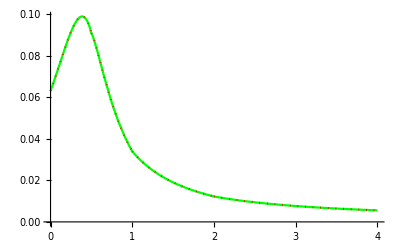

```mathematica
p1S=Plot[ϕ1S[s1,r,t1],{r,0,s1},PlotStyle->{Red,Dotted}];
p1L=Plot[ϕ1L[s1,r,t1],{r,s1,r0},PlotStyle->{Red,Dotted}];
p12=Plot[ϕ12[s1,r,t1],{r,r0,R},PlotStyle->{Red,Dotted}];
p13=Plot[ϕ13[s1,r,t1],{r,R,2*R},PlotStyle->{Red,Dotted}];
(*Plot[ϕ1[s1,r,t1],{r,r0/3,2*r0/3}](*cusp due to slow convergence of the sums*)*)
p1=Plot[ϕ1[s1,r,t1],{r,0,2*R},PlotStyle->{Green}];
Show[p1,p1S,p1L,p12,p13]
```

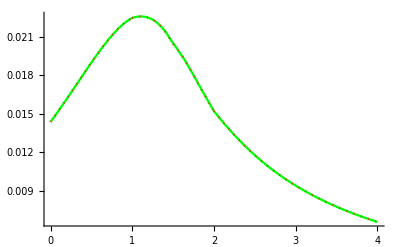

```mathematica
p21=Plot[ϕ21[s2,r,t2],{r,0,r0},PlotStyle->{Red,Dotted}];
p2S=Plot[ϕ2S[s2,r,t2],{r,r0,s2},PlotStyle->{Red,Dotted}];
p2L=Plot[ϕ2L[s2,r,t2],{r,s2,R},PlotStyle->{Red,Dotted}];
p23=Plot[ϕ23[s2,r,t2],{r,R,2*R},PlotStyle->{Red,Dotted}];
p2=Plot[ϕ2[s2,r,t2],{r,0,2*R},PlotRange->All,AxesOrigin->{0,0},PlotStyle->{Green}];
Show[p2,p21,p2S,p2L,p23]
```

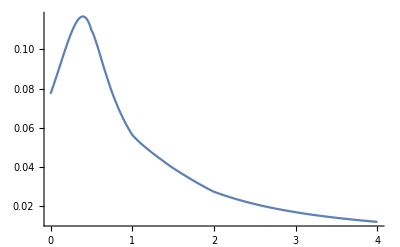

```mathematica
Plot[ϕ1[s1,r,t1]+ϕ2[s2,r,t2],{r,0,2*R},PlotRange->All,AxesOrigin->{0,0}]
```

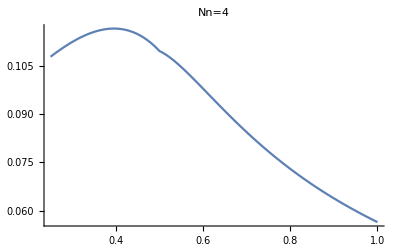

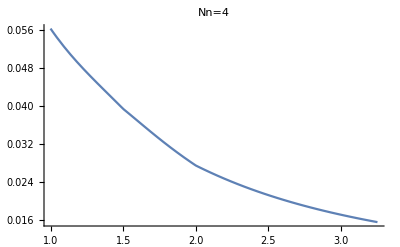

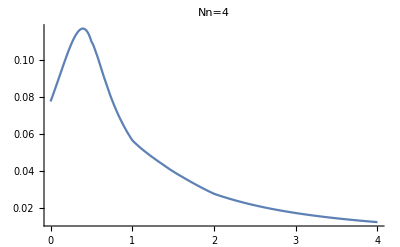

```mathematica
(*Nn=4*)
Plot[ϕ1[s1,r,t1]+ϕ2[s2,r,t2],{r,s1/2,r0},PlotRange->All,AxesOrigin->{0,0},PlotLabel->"Nn=4"]
Plot[ϕ1[s1,r,t1]+ϕ2[s2,r,t2],{r,r0,r0+3*s2/2},PlotRange->All,AxesOrigin->{0,0},PlotLabel->"Nn=4"]
Plot[ϕ1[s1,r,t1]+ϕ2[s2,r,t2],{r,0,2*R},PlotRange->All,AxesOrigin->{0,0},PlotLabel->"Nn=4"]
```

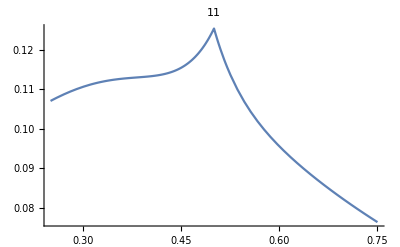

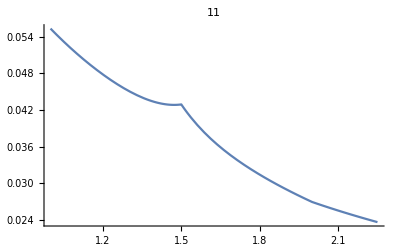

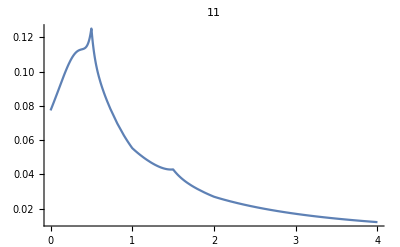

```mathematica
Nn=452;
Nn=11;
Plot[ϕ1[s1,r,t1]+ϕ2[s2,r,t2],{r,s1/2,3*s1/2},PlotRange->All,AxesOrigin->{0,0},PlotLabel->Nn]
Plot[ϕ1[s1,r,t1]+ϕ2[s2,r,t2],{r,r0,3*s2/2},PlotRange->All,AxesOrigin->{0,0},PlotLabel->Nn]
Plot[ϕ1[s1,r,t1]+ϕ2[s2,r,t2],{r,0,2*R},PlotRange->All,AxesOrigin->{0,0},PlotLabel->Nn](**)
```

```mathematica
Clear[r0, R,ϵ0,ϵ1,ϵ2,ϵ3,s1,s2,q1,q2,Nn];
```

## 7.2 Check ϕ_1+ϕ_2 convergence with the parameters from 7.1

Potential for Nn=29

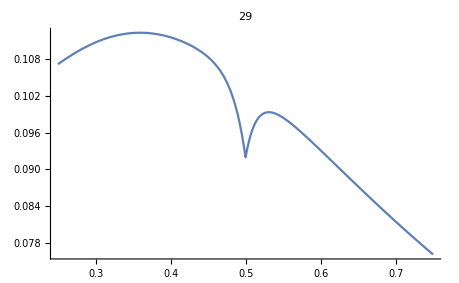
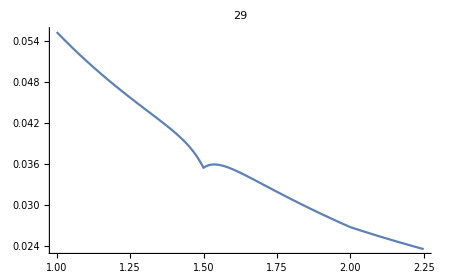
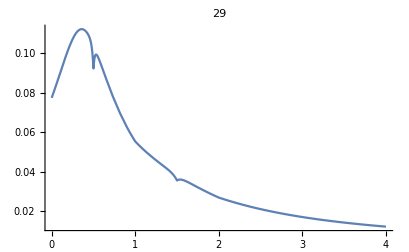

Potential for Nn=129

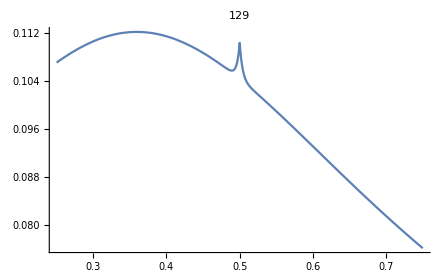
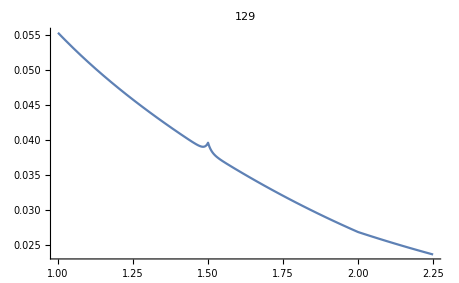
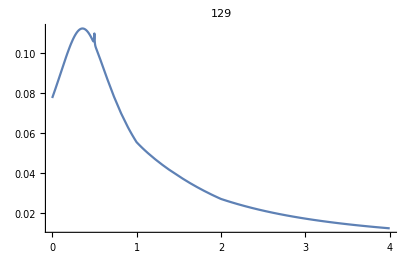

Potential for Nn=229

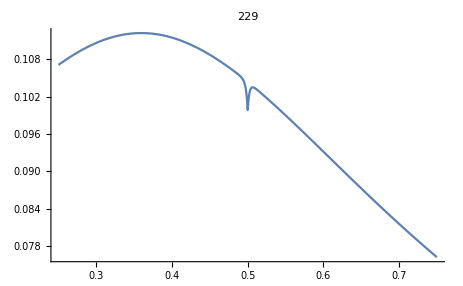
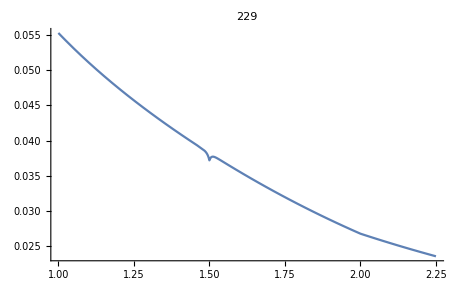
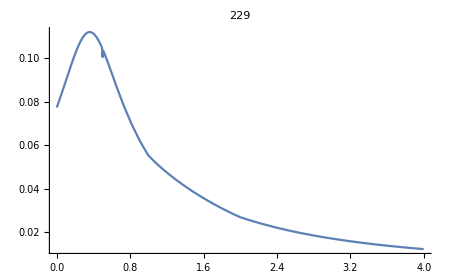

Potential for Nn=329

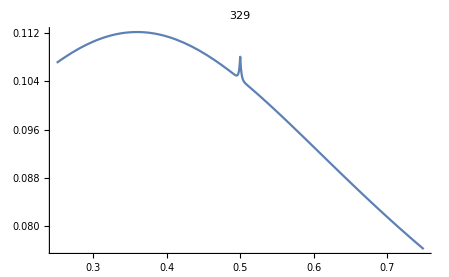
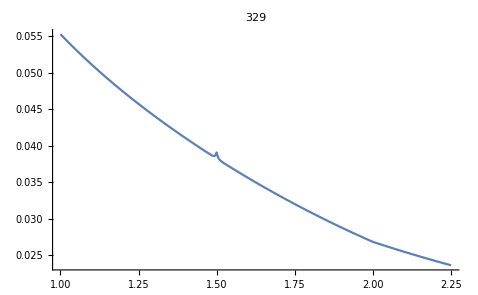
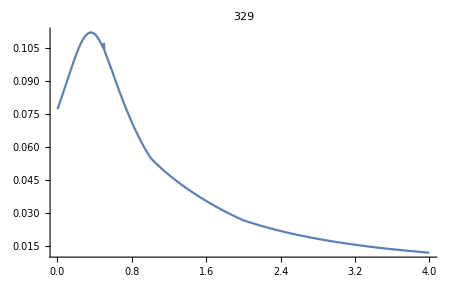

Potential for Nn=451

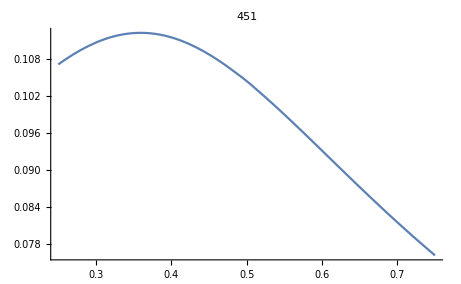
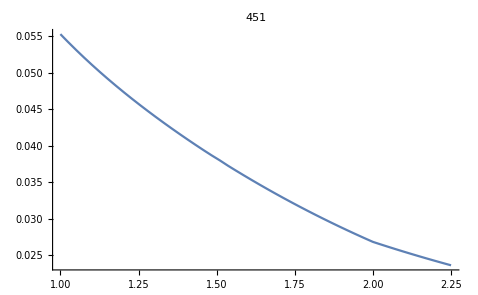
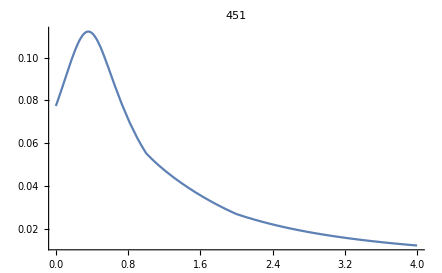

Potential for Nn=452

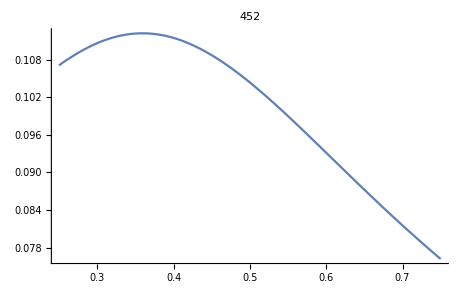
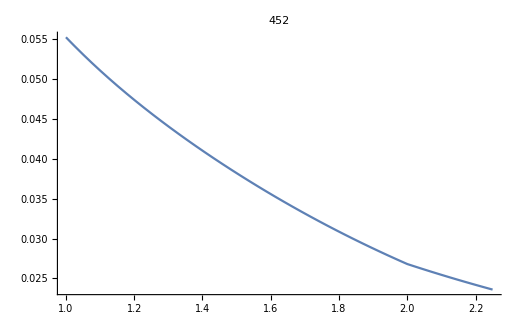
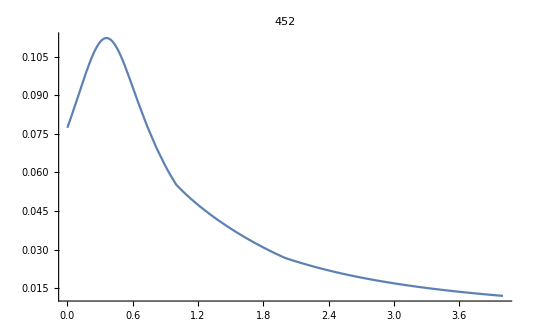

# 8. Polarization charge

-Graphics-
Fig .4

```mathematica
(*POTENTIALS for the geometry from Fig.4*)

P[n_,θ_]:=LegendreP[n,Cos[θ]];
PA[n_,m_,θ_]:=LegendreP[n,m,Cos[θ]];
(*eq. 19:*)
PP[n_,θ_,α_,φ_,β_]:=P[n,θ]*P[n,α]+2*∑_(m=1)^n (((n-m)!)/((n+m)!)*PA[n,m,θ]*PA[n,m,α]*Cos[m*(φ-β)]);
ϕ1L[s1_,r_,θ_,θ1_,φ_,φ1_]:=∑_(n=0)^Nn (q1/(4*π*ϵ0*ϵ1*r)(s1/r)^n+A1[n]*r^n)*PP[n,θ,θ1,φ,φ1];
ϕ12[s1_,r_,θ_,θ1_,φ_,φ1_]:=∑_(n=0)^Nn (B1[n]*r^n+C1[n]*r^(-n-1))*PP[n,θ,θ1,φ,φ1];
ϕ13[s1_,r_,θ_,θ1_,φ_,φ1_]:=∑_(n=0)^Nn D1[n]*r^(-n-1)*PP[n,θ,θ1,φ,φ1];
ϕ21[s2_,r_,θ_,θ2_,φ_,φ2_]:=∑_(n=0)^Nn A2[n]*r^n*PP[n,θ,θ2,φ,φ2];
ϕ2S[s2_,r_,θ_,θ2_,φ_,φ2_]:=∑_(n=0)^Nn (q2/(4*π*ϵ0*ϵ2*s2)*(r/s2)^n+B2[n]*r^n+C2[n]*r^(-n-1))*PP[n,θ,θ2,φ,φ2];
ϕ2L[s2_,r_,θ_,θ2_,φ_,φ2_]:=∑_(n=0)^Nn (q2/(4*π*ϵ0*ϵ2*r)(s2/r)^n+B2[n]*r^n+C2[n]*r^(-n-1))*PP[n,θ,θ2,φ,φ2];
ϕ23[s2_,r_,θ_,θ2_,φ_,φ2_]:=∑_(n=0)^Nn D2[n]*r^(-n-1)*PP[n,θ,θ2,φ,φ2];
```

```mathematica
(*FIELDS for the geometry from Fig.4*)
E1L[s1_,r_,θ_,θ1_,φ_,φ1_]:=-D[ϕ1L[s1,r,θ,θ1,φ,φ1],r];
E12[s1_,r_,θ_,θ1_,φ_,φ1_]:=-D[ϕ12[s1,r,θ,θ1,φ,φ1],r];
E13[s1_,r_,θ_,θ1_,φ_,φ1_]:=-D[ϕ13[s1,r,θ,θ1,φ,φ1],r];

E21[s2_,r_,θ_,θ2_,φ_,φ2_]:=-D[ϕ21[s2,r,θ,θ2,φ,φ2],r];
E2S[s2_,r_,θ_,θ2_,φ_,φ2_]:=-D[ϕ2S[s2,r,θ,θ2,φ,φ2],r];
E2L[s2_,r_,θ_,θ2_,φ_,φ2_]:=-D[ϕ2L[s2,r,θ,θ2,φ,φ2],r];
E23[s2_,r_,θ_,θ2_,φ_,φ2_]:=-D[ϕ23[s2,r,θ,θ2,φ,φ2],r];

σ12[s1_,s2_,θ_,θ1_,θ2_,φ_,φ1_,φ2_]:=-(χ2*E12[s1,r,θ,θ1,φ,φ1]-χ1*E1L[s1,r,θ,θ1,φ,φ1]+χ2*E2S[s2,r,θ,θ2,φ,φ2]-χ1*E21[s2,r,θ,θ2,φ,φ2])/.r->r0;
σ23[s1_,s2_,θ_,θ1_,θ2_,φ_,φ1_,φ2_]:=-(χ3*E13[s1,r,θ,θ1,φ,φ1]-χ2*E12[s1,r,θ,θ1,φ,φ1]+χ3*E23[s2,r,θ,θ2,φ,φ2]-χ2*E2L[s2,r,θ,θ2,φ,φ2])/.r->R;
```

```mathematica
r0=1.; R=2*r0;s1=r0/2;s2=3*r0/2;

(*---------------------*)
ϵ0=1;ϵ1=2;ϵ2=3;ϵ3=4;
q1=1;q2=1;
(*---------------------*)
(*---------------------*)
(* check with Jackson (4.47), p.157: *)
ϵ0=1;ϵ1=4;ϵ2=1;ϵ3=1;
q1=1;q2=0;
(*---------------------*)

χ1=ϵ1-1;
χ2=ϵ2-1;
χ3=ϵ3-1;
Nn=5;
θ1=Pi-Pi/6;
θ2=Pi-Pi/4;
φ1=0;
φ2=4*Pi/3;
(*---------------------*)

θ=π/4;
φ=π/4;
Print["σ12[s1,s2,θ=π/4,θ1,θ2,φ=π/4]=",σ12[s1,s2,θ,θ1,θ2,φ,φ1,φ2]];
Print["σ23[s1,s2,θ=π/4,θ1,θ2,φ=π/4]=",σ23[s1,s2,θ,θ1,θ2,φ,φ1,φ2]];
Clear[θ,φ];
```

σ12[s1,s2,θ=π/4,θ1,θ2,φ=π/4]=0.046433

σ23[s1,s2,θ=π/4,θ1,θ2,φ=π/4]=0

```mathematica
Nn=10;
ϵ0=1;ϵ1=8;ϵ2=8;ϵ3=12;
Desig={"a)","b)","c)","d)"};
Q1={0,-1,0,-1};
Q2={1,1,1,1};
Phi1={Pi/6,0,0,0};
Theta1={Pi/3,0,0,0};
Phi2={Pi/3,0,0,0};
Theta2={Pi/6,0,0,Pi/2};
For[i=1,i<=1,i++,
φ1=Phi1[[i]];
φ2=Phi2[[i]];
θ1=Theta1[[i]];
θ2=Theta2[[i]];
q1=Q1[[i]];
q2=Q2[[i]];
(*
Tσ=Flatten[Table[{σ12[s1,s2,θ,θ1,θ2,φ,φ1,φ2],σ23[s1,s2,θ,θ1,θ2,φ,φ1,φ2]},{φ,0, 2π},{θ,0,π}],2];
Print["minσ=",minσ=Min[Tσ]];
Print["maxσ=",maxσ=Max[Tσ]];
*)
minσ12=First[NMinimize[{σ12[s1,s2,θ,θ1,θ2,φ,φ1,φ2],0<=φ<=2π,0<=θ<=π},{φ,θ},AccuracyGoal->9,PrecisionGoal->8,WorkingPrecision->10,Method->"SimulatedAnnealing"]];
maxσ12=First[NMaximize[{σ12[s1,s2,θ,θ1,θ2,φ,φ1,φ2],0<=φ<=2π,0<=θ<=π},{φ,θ},AccuracyGoal->9,PrecisionGoal->8,WorkingPrecision->10,Method->"SimulatedAnnealing"]];
minσ23=First[NMinimize[{σ23[s1,s2,θ,θ1,θ2,φ,φ1,φ2],0<=φ<=2π,0<=θ<=π},{φ,θ},AccuracyGoal->9,PrecisionGoal->8,WorkingPrecision->10,Method->"SimulatedAnnealing"]];
maxσ23=First[NMaximize[{σ23[s1,s2,θ,θ1,θ2,φ,φ1,φ2],0<=φ<=2π,0<=θ<=π},{φ,θ},AccuracyGoal->9,PrecisionGoal->8,WorkingPrecision->10,Method->"SimulatedAnnealing"]];
(*Do not use NelderMead! The other methods give the same results as far as we tested*)
Print["minσ=",minσ=Min[minσ12,minσ23]];
Print["maxσ=",maxσ=Max[maxσ12,maxσ23]];
(*minσ=Min[Tσ];
maxσ=Max[Tσ];*)
Print[p1=ParametricPlot3D[r0*{Cos[φ]*Sin[θ],Sin[φ]*Sin[θ],Cos[θ]},{φ,0, 2π},{θ,0,π},Mesh->False,ColorFunction->(Function[{x,y,z,φ,θ},ColorData["TemperatureMap"][Rescale[σ12[s1,s2,θ,θ1,θ2,φ,φ1,φ2],{minσ,maxσ}]]]),
PlotStyle->Directive[(*GrayLevel[0],*)Opacity[0.6]],ColorFunctionScaling->False,PlotLegends->BarLegend[{ColorData["TemperatureMap"],{minσ,maxσ}},ColorFunctionScaling->True,LabelStyle->Directive[20,Bold],LegendLayout->"Column",LegendMarkerSize->300,Ticks->{-0.15,-0.1,-0.05,-0.02,0,0.02,0.05,0.1,0.15}],Axes->None,Boxed->False,Ticks->None,ViewAngle->Pi/12,PlotLabel->Style[Desig[[i]],Bold,40]]];
Print[p2=ParametricPlot3D[R*{Cos[φ]*Sin[θ],Sin[φ]*Sin[θ],Cos[θ]},{φ,0,π},{θ,0,π},Mesh->False,ColorFunction->(Function[{x,y,z,φ,θ},ColorData["TemperatureMap"][Rescale[σ23[s1,s2,θ,θ1,θ2,φ,φ1,φ2],{minσ,maxσ}]]]),
PlotStyle->Directive[(*GrayLevel[0],*)Opacity[0.6]],ColorFunctionScaling->False,Boxed->False,Axes->False]];
Print[p3=ListPointPlot3D[{{s1*Sin[θ1]*Cos[φ1],s1*Sin[θ1]*Sin[φ1],s1*Cos[θ1]},{s2*Sin[θ2]*Cos[φ2],s2*Sin[θ2]*Sin[φ2],s2*Cos[θ2]}},PlotStyle->Directive[Black,PointSize[0.03]],Boxed->False,Axes->False]];
p4=Graphics3D[{If[θ2≠0,{Dashed,Thick,Line[{{0,0,0},{s2*Sin[θ2]*Cos[φ2],s2*Sin[θ2]*Sin[φ2],s2*Cos[θ2]}}]},],If[θ1≠0,{Dashed,Thick,Line[{{0,0,0},{s1*Sin[θ1]*Cos[φ1],s1*Sin[θ1]*Sin[φ1],s1*Cos[θ1]}}]},],Text[Style["x",32],{2.35,-0.15,0}],Text[Style["y",32],{-0.2,2.4,0}],Text[Style["z",32],{0,0,2.4}],{Thick,{Arrowheads[.025],Arrow[{{0,0,0},{0,2.3,0}}]}},{Thick,{Arrowheads[.025],Arrow[{{0,0,0},{2.3,0,0}}]}},{Thick,{Arrowheads[.025],Arrow[{{0,0,0},{0,0,2.15}}]}}}];

Print[Show[p1,p2,p3,p4,PlotRange->All]]]
```

minσ=-0.1070379956

maxσ=0.005136258811

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

TO ADD in the figures:
AXES AS IN FIG. 4 
COLOR LEGENDA (vezi mai jos).

Figuri:
1) α=0, cu 1a: q1=-1&q2=-1, 1b: q1=-1&q2=0, 1c: q1=-1&q2=1, 1d: q1=0&q2=-1, 1e:q1=0&q2=0, 1f: q1=0&q2=1,
1g: q1=1&q2=-1, 1g: q1=1&q2=0, 1h: q1=1&q2=1;
2) α=Pi/2, etc.
3) α=Pi, etc.
	 
Pt fiecare caz in parte, de ex., 1)1a (eu am selectat 3x4, in aldine, din cele 3x8 cazuri, ar merge la Appendix) faceti o 'normare' a culorii: gasiti din cele doua tabele de date,  (vezi p1 si p2), maximul |σ(x,y,z)| = max si apoi pt fiecare (x,y,z) calculati σ(x,y,z)/max care va fi valoarea fctiei de culoare in punctul (x,y,z);  fctia de culoare pt orice (x,y,z) este in intervalul [-1,1], deci de aici trebuie plecat pt a selecta cea mai potrivita comanda Mathematica pt culoare.

(*
Example:
https://mathematica.stackexchange.com/questions/52234/add-a-color-bar-legend-to-a-3d-plot

{min,max}={-10,10};
h2=ParametricPlot3D[lst,{u,0,2*Pi},{v,0,Pi},Mesh→False,ColorFunction→(Function[{x,y,z,u,v},Hue[Rescale[dam,{0,1}]]]),ColorFunctionScaling→False,ImageSize→800,PlotLegends→BarLegend[{Hue,{min,max}},ColorFunctionScaling→True]]
*)
(**)